```mathematica
Clear["Global`*"];
ssx1i={};
ssx1d={};
ssx2i={};
ssx2d={};
ssx3i={};
ssx3d={};
ssx4i={};
ssx4d={};
ssx5i={};
ssx5d={};
ssx6i={};
ssx6d={};
ssin={};
(* Initialize all the equations and parameters *)
sTot=9.993526721 ;eTot=2.113066106 ;
dEs={D[x1[t],t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t],D[x2[t],t]==k3*x5[t]+k6*x6[t]-k7*x2[t],D[x3[t],t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t],D[x4[t],t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t],D[x5[t],t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t],D[x6[t],t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]};
invaEs={x1[t]+x2[t]+x5[t]+x6[t]==sTot,x3[t]+x4[t]+x5[t]+x6[t]==eTot};
(*params:1076 86.77935589 3.583044479 92.84145445 1.199993478 0.026263635 0.264415792 2.357404008 0.013100928 0.784202374 1.041346611 0.008056722 9.993526721 2.113066106 67.99832459 3.39384643 8630344 *)
(* Get the steady state first *)
tf=50000;
input=80;
icEs={x1[0]==sTot,x2[0]==0,x3[0]==eTot,x4[0]==0,x5[0]==0,x6[0]==0};
params = {k1->86.77935589,k2->3.583044479,k3->input,k4->1.199993478,k5->0.026263635,k6->0.264415792,k7->2.357404008,k8->0.013100928,k9->0.784202374,k10->1.041346611,k11->0.008056722};

sol=NDSolve[{dEs,icEs}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

For[i=0,i≤400,i++,
tf=50000;

input=80+i*0.1;
params = {k1->86.77935589,k2->3.583044479,k3->input,k4->1.199993478,k5->0.026263635,k6->0.264415792,k7->2.357404008,k8->0.013100928,k9->0.784202374,k10->1.041346611,k11->0.008056722};

newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};

sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

ssx1i=Append[ssx1i,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2i=Append[ssx2i,Evaluate[x2[tf]/.sol][[1]]];ssx3i=Append[ssx3i,Evaluate[x3[tf]/.sol][[1]]];ssx4i=Append[ssx4i,Evaluate[x4[tf]/.sol][[1]]];ssx5i=Append[ssx5i,Evaluate[x5[tf]/.sol][[1]]];ssx6i=Append[ssx6i,Evaluate[x6[tf]/.sol][[1]]];
];

For[i=0,i≤400,i++,
tf=50000;

input=120-i*0.1;
params = {k1->86.77935589,k2->3.583044479,k3->input,k4->1.199993478,k5->0.026263635,k6->0.264415792,k7->2.357404008,k8->0.013100928,k9->0.784202374,k10->1.041346611,k11->0.008056722};

newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};

sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

ssx1d=Append[ssx1d,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2d=Append[ssx2d,Evaluate[x2[tf]/.sol][[1]]];ssx3d=Append[ssx3d,Evaluate[x3[tf]/.sol][[1]]];ssx4d=Append[ssx4d,Evaluate[x4[tf]/.sol][[1]]];ssx5d=Append[ssx5d,Evaluate[x5[tf]/.sol][[1]]];ssx6d=Append[ssx6d,Evaluate[x6[tf]/.sol][[1]]];
];
```

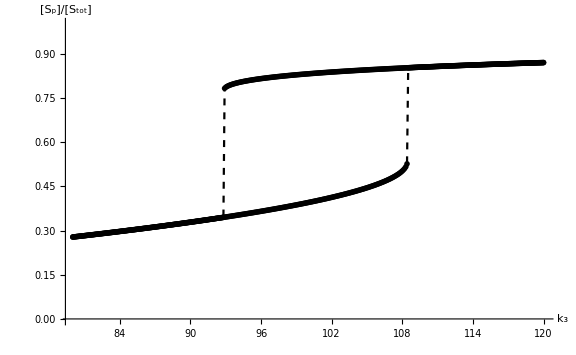

```mathematica
ListLinePlot[{Transpose@{Range[80,120,0.1],ssx2i/sTot},Transpose@{Range[80,120,0.1],Reverse[ssx2d/sTot]}},PlotTheme->"Monochrome",PlotStyle->{{Dashed},{Dashed}}, AxesLabel->{RawBoxes[RowBox[{SubscriptBox["k","3"]}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->{0,1}]
```

```mathematica
ListPlot[{Transpose@{Range[80,120,0.1],ssx2i/sTot},Transpose@{Range[80,120,0.1],Reverse[ssx2d/sTot]}},PlotTheme->"Monochrome",PlotMarkers->{"●","●"},AxesLabel->{RawBoxes[RowBox[{SubscriptBox["k","3"]}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->{0,1}]
```

-Graphics-

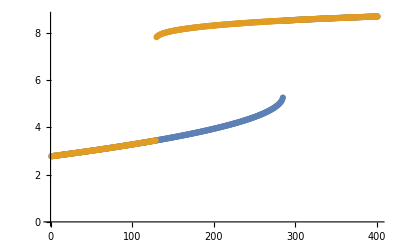

```mathematica
ListPlot[{ssx2i,Reverse[ssx2d]},PlotRange->Full]
```

```mathematica
?PlotStyle
```

PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn.

```mathematica
ListLinePlot[{Transpose@{Range[80,120,0.1],ssx2i/sTot},Transpose@{Range[80,120,0.1],Reverse[ssx2d/sTot]}},PlotTheme->"Monochrome",PlotStyle->{{Dashed},{Dashed}},PlotMarkers->{"●","●"}, AxesLabel->{RawBoxes[RowBox[{SubscriptBox["k","3"]}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]","/","[",SubscriptBox["S","tot"],"]"}]]},LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->{0,1}]
```

-Graphics-

```mathematica
●//InputForm
```

●